```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/GAelectrodynamics-figures" ]
```

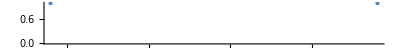

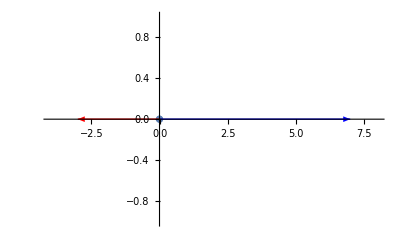

{1DnumberlineFig1.eps,1DnumberlineFig1pn.png}

{1DarrowsFig2.eps,1DarrowsFig2pn.png}

```mathematica
p1 = -3;
p2 = 7;
o = {0,0};
a1 = {p1,0};
a2 = {p2,0};

n=NumberLinePlot[{p1,p2}]
pts = ListPlot[{o(*,a1,a2*)}, PlotRange->{{-4,8},{-1,1}}, Axes ->{Automatic,None}];
arrows = Graphics[{Thick,
Red,Arrow[{o,a1}],
Blue, Arrow[{o,a2}]}
];

s = Show[pts,arrows]
peeters`exportForLatex["1DnumberlineFig1", n]
peeters`exportForLatex["1DarrowsFig2", s]
```

```mathematica
Directory[]
```

/Users/pjoot/project/GAelectrodynamics-figures